# Mathematica Homework

## 中山大学物理学院，广东，广州

郭蒙 20343097

1. Use the Basic Input palette to type in the expression 3100 below this cell. Hit ⇧|⏎ together to evaluate this expression. Note that you should get the exact answer.

```mathematica
3^100
```

515377520732011331036461129765621272702107522001

2. Select your input line above (either by selecting its Computational Biophysics cell bracket or by scrolling over the expression with the mouse clicked) and make a copy using Copy
under the Edit menu. Paste your expression below this box. Change the 100 to 1000 and evaluate the result.

```mathematica
5^1000
```

933263618503218878990089544723817169617091446371708024621714339795966910975775634454440327097881102359594989930324242624215487521354032394841520817203930756234410666138325150273995075985901831511100490796265113118240512514795933790805178271125415103810698378854426481119469814228660959222017662910442798456169448887147466528006328368452647429261829862165202793195289493607117850663668741065439805530718136320599844826041954101213229629869502194514609904214608668361244792952034826864617657926916047420065936389041737895822118365078045556628444273925387517127854796781556346403714877681766899855392069265439424008711973674701749862626690747296762535803929376233833981046927874558605253696441650390625

3.  To get the result in the form you might get on a calculator, try N[%].

```mathematica
N[%]
```

9.33263618503219×10^698

4. Enter pi = N[π, 200] below this cell and evaluate it

```mathematica
pi=N[Pi,200]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930382

5. Enter ⅇ163 pi3 below this cell and evaluate it. What is special about this number?

```mathematica
E^(√163 Pi/3)
```

ⅇ^((√163 π)/3)

```mathematica
N[ⅇ^((√163 π)/3),200]
```

640320.00000000060486373504901603947174181881853947577148576036659181946522182582869425363408158226464775899925470001727925679647867303997506923198495665261269396826561338913713441824901972334433095988

6. π has a run of six consecutive 9’s in the first 1000 digits. Can you see where they are located? (One way to find the location is to convert the number to a 2 HomeWork.nb string [using ToString], drop the leading 3. [using StringDrop] and locating the position of the string “999999” [using StringPosition]).

```mathematica
ToString[N[Pi]]
```

3.14159

7. Compute sin(13 π), log(2.1), and ⅇⅈ π by copying these expressions below this cell and entering them.

```mathematica
MatrixForm[{Sin[13 Pi],Log[2,1],E^(I Pi)}]
```

(0
0
-1)

8. Lookup cos in the on-line help and determine closed-form expressions for cos( π5 ).

```mathematica
Cos[Pi/5]
```

1/4 (1+√5)

9. Evaluate FactorInteger[70 612 139 395 722 186]. What is the meaning of this output?

```mathematica
FactorInteger[70612139395722186]
```

{{2,1},{3,2},{43,5},{26684839,1}}

10. Recombine the numbers in the above output to show how they form 70 612 139 395 722 186.

```mathematica
2^1 3^2 43^5 26684839
```

70612139395722186

11. Enter the expression (x2 + 2 x + 1)20. Expand this

```mathematica
expres1=(x^2+2x+1)^20;
Expand[expres1]
```

1+40 x+780 x^2+9880 x^3+91390 x^4+658008 x^5+3838380 x^6+18643560 x^7+76904685 x^8+273438880 x^9+847660528 x^10+2311801440 x^11+5586853480 x^12+12033222880 x^13+23206929840 x^14+40225345056 x^15+62852101650 x^16+88732378800 x^17+113380261800 x^18+131282408400 x^19+137846528820 x^20+131282408400 x^21+113380261800 x^22+88732378800 x^23+62852101650 x^24+40225345056 x^25+23206929840 x^26+12033222880 x^27+5586853480 x^28+2311801440 x^29+847660528 x^30+273438880 x^31+76904685 x^32+18643560 x^33+3838380 x^34+658008 x^35+91390 x^36+9880 x^37+780 x^38+40 x^39+x^40

12. Re-do the steps in the above computation using the Basic Calculations palette.

```mathematica
(x^2+2x+1)^2
```

(1+2 x+x^2)^2

13. TrigReduce[sin(x) cos(y) - cos(x) sin(y)] and apply TrigExpand to the result. What can you say about the relationship between these functions?

```mathematica
Clear[x,y]
TrigReduce[Sin[x]Cos[y]-Cos[x]Sin[y]]
```

Sin[x-y]

14. Produce a plot of sin(x2) over x ∈ [0, 5]

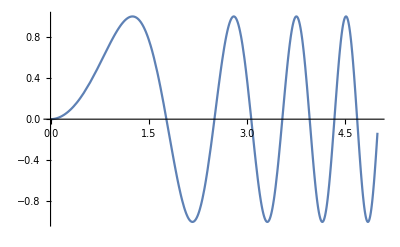

```mathematica
Plot[Sin[x^2],{x,0,5}]
```

15. Produce a phase-space plot of cos(x) versus sin(3 x) for over x ∈ [0, 2 π].

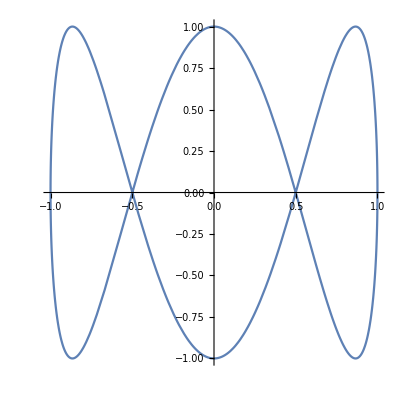

```mathematica
ParametricPlot[{Cos[x],Sin[3x]},{x,0,2 Pi}]
```

16. Produce a contour plot and density plot of x ⅇ-x2-y2 4 HomeWork.nb for -1 ≤ x ≤ 1 and -1 ≤ y ≤ 1

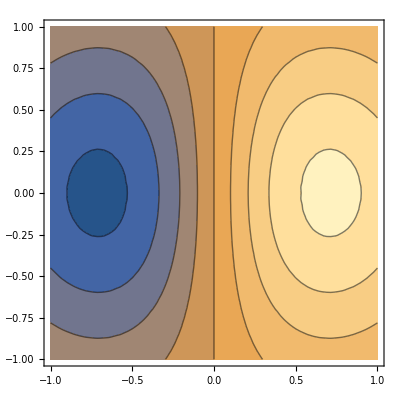

```mathematica
Clear[x,y]
ContourPlot[x E^(-x^2-y^2),{x,-1,1},{y,-1,1}]
```

17. Compute ∫x/(x^3-1)ⅆx.Check by differentiating the resulting expression with respect to  and then using Simplify.

```mathematica
∫x/(x^3-1)ⅆx
```

```mathematica
ArcTan[(1+2 x)/(√3)]/(√3)+1/3 Log[1-x]-1/6 Log[1+x+x^2]
```

We then differentiate it and simplify to check out.

```mathematica
D[ArcTan[(1+2 x)/(√3)]/(√3)+1/3 Log[1-x]-1/6 Log[1+x+x^2],x]//Simplify
```

x/(-1+x^3)

We can see the result and the expectation fits well.

18.  Compute ∫_0^∞ (sin^2(x)cos^2(x))/x ⅆx

```mathematica
N[Integrate[(Sin[x]^2 Cos[x]^2)/x,{x,0,∞}]]
```

1.98723

19. Try ∫_0^1 sin(sin(x))ⅆx.Compute the numerical value of this expression using N[%]

```mathematica
Integrate[Sin[Sin[x]],{x,0,1}];
N[%]
```

```mathematica
Integrate[Sin[Sin[x]],{x,0,π}]
```

π StruveH[0,1]

20. Use Solve to obtain the roots of the quadratic equation a x^2 + b x + c = 0, and call the set of solutions s. Check the solutions by back-substitution using the syntax a x2 + b x + c /. s. You will need to Simplify the result

```mathematica
s= Solve[a x^2+b x+c==0,x]
a x^2+b x +c /.s//Simplify
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

{0,0}

21. Solve the cubic equation x^3 - x + 1 == 0. Evaluate this expression numerically using N. Does your answer satisfy the requirement that roots of equations with real coefficients must come in conjugate pairs (a conjugate pair is a set of two numbers of the form a±b ⅈ)

```mathematica
NSolve[x^3-x+1==0,x]
```

{{x→-1.32472},{x→0.662359-0.56228 ⅈ},{x→0.662359+0.56228 ⅈ}}

The 0.662359-0.56228 ⅈ and 0.662359+0.56228 ⅈ come with pairs.

22. In a new cell, enter the 2×2 matrix,mat = (3.5 | 7.2
-2.4 | 6.4).Compute the inverse and eigenvalues of mat—— you should be able to guess the names of the appropriate Mathematica commands.

```mathematica
mat={{3.5,7.2},{-2.4,6.4}}
invermat=Inverse[mat]
Eigenvalues[mat]
```

{{3.5,7.2},{-2.4,6.4}}

{{0.16129,-0.181452},{0.0604839,0.0882056}}

{4.95+3.89583 ⅈ,4.95-3.89583 ⅈ}

23. Enter mat = (a | b | c
d | e | f
g | h | i).This overwrites your previous value of the matrix mat.Compute the inverse of mat and assign (using =) the result to minv. Compute minv.mat and simplify the result

```mathematica
mat={{a,b,c},{d,e,f},{g,h,i}};
minv=Inverse[mat];
minv//MatrixForm
minv.mat//Simplify//MatrixForm
```

((-f h+e i)/(-c e g+b f g+c d h-a f h-b d i+a e i) | (c h-b i)/(-c e g+b f g+c d h-a f h-b d i+a e i) | (-c e+b f)/(-c e g+b f g+c d h-a f h-b d i+a e i)
(f g-d i)/(-c e g+b f g+c d h-a f h-b d i+a e i) | (-c g+a i)/(-c e g+b f g+c d h-a f h-b d i+a e i) | (c d-a f)/(-c e g+b f g+c d h-a f h-b d i+a e i)
(-e g+d h)/(-c e g+b f g+c d h-a f h-b d i+a e i) | (b g-a h)/(-c e g+b f g+c d h-a f h-b d i+a e i) | (-b d+a e)/(-c e g+b f g+c d h-a f h-b d i+a e i))

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

24. Generate a random real 3×3 matrix and call it rand (Hint: use Random and Table). Replace the {2, 2} entry of rand with the symbolic parameter x. Compute the (symbolic) inverse of rand and determine the numerical value of the inverse when x → 1.

```mathematica
Clear[x];
rand=RandomReal[{-10,10},{2,2}];
randx=ReplacePart[rand,{2,2}->x];
randx//MatrixForm
Eigenvalues[randx/.x->1]
```

(-6.00256 | 7.55289
6.17562 | x)

{-10.1761,5.17353}

25.Use the command Table[i!, {i, 1, 10}] to compute the first 10 values of the factorial function and assign the answer to the variable called is

```mathematica
is=Table[i!,{i,1,10}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

26. Take the log of values using log(is) and numerically evaluate the result. Save this result as a named variable called data

```mathematica
data=Log[is]//N
```

{0.,0.693147,1.79176,3.17805,4.78749,6.57925,8.52516,10.6046,12.8018,15.1044}

27. Use ListPlot to plot data and save your graphic as a named variable called, e.g., p1

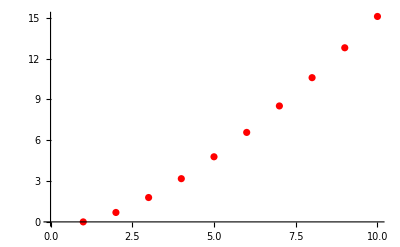

```mathematica
p1=ListPlot[data,PlotStyle->Red]
```

28. Compute the best (least-squares) third-order polynomial fit to this data using Fit. Obtain a plot of this fit and call it p2. You need to choose and appropriate range for the Plot command (see PlotRange). Show p1 and p2 superimposed using Show.

-0.158921+0.238644 x^2-0.00866872 x^3

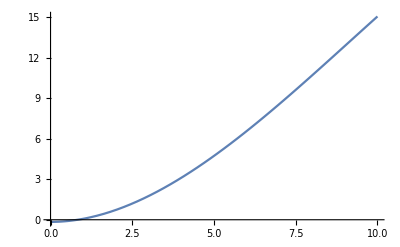

```mathematica
fitting=Fit[data,{1,x^2,x^3},x]
p2=Plot[fitting,{x,0,10}]
```

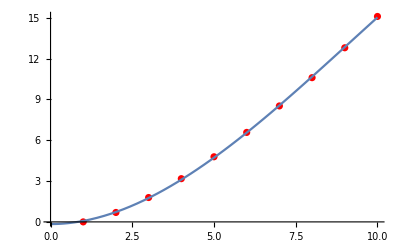

```mathematica
Show[p1,p2]
```

29. Plot animations of 2 D Curve and 3 D Surface.

```mathematica
frames=Animate[Plot3D[Re@Sin[x+I*y],{x,-10,10},{y,-10,10},Mesh->{{{0,None}},{{i,{Red,Thick}}}}],{i,-10,10,.5}]
```

30.Processing an image

```mathematica
Export["test.gif",%]
```

test.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["test.gif"]]]
```